Root Locus Parameters

1. Open-Loop Poles (n=3): {-4,-2,0}

2. Open-Loop Zeros (m=0): {}

3. Number of Asymptotes (n-m): 3

4. Asymptote Centroid (σ): -2

5. Asymptote Angles (θ): {π/3,π,(5 π)/3} (in Radians)

6. Breakaway/Break-in Points: {-3.1547,-0.845299}

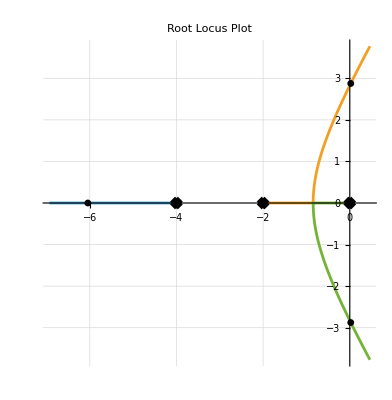

```mathematica
Clear[s,GH,k];

(*Define the Open-Loop Transfer Function*)
GH=1/(s*(s+2)*(s+4));

(*Simplify the transfer function and extract numerator and denominator*)
num=Numerator[Cancel[GH]];
den=Denominator[Cancel[GH]];

(*Safe Extraction of Poles (K=0) and Zeros (K=∞)*)
pSol=Solve[den==0,s];
poles=If[Length[pSol]==0,{},s/. pSol];

zSol=Solve[num==0,s];
zeros=If[Length[zSol]==0,{},s/. zSol];

n=Length[poles];
m=Length[zeros];

(*Rule 5:Calculate Centroid (σ) of Asymptotes*)
centroid=If[n>m,Simplify[(Total[poles]-Total[zeros])/(n-m)],"N/A (n <= m)"];

(*Asymptote Angles (θ_q)*)
angles=If[n>m,Table[Simplify[(2 q+1) Pi/(n-m)],{q,0,n-m-1}],"N/A"];

(*Rule 8:Safe Extraction of Breakaway/Break-in Points*)
bSol=Solve[D[GH,s]==0,s];
breakawayPts=If[Length[bSol]==0,{},s/. bSol];

(*Print the calculated parameters cleanly*)
Print[Style["Root Locus Parameters",Bold,14]];
Print["1. Open-Loop Poles (n=",n,"): ",poles];
Print["2. Open-Loop Zeros (m=",m,"): ",zeros];
Print["3. Number of Asymptotes (n-m): ",n-m];
Print["4. Asymptote Centroid (σ): ",centroid];
Print["5. Asymptote Angles (θ): ",angles," (in Radians)"];
Print["6. Breakaway/Break-in Points: ",N[breakawayPts]];

(*Built-in visualization:Convert to TransferFunctionModel for accurate plotting*)
(*Explicitly include the gain parameter'k' inside the system*)

RootLocusPlot[k*GH,{k,0,100},PlotLabel->"Root Locus Plot",PlotRange->All,GridLines->Automatic]
```

```mathematica
poly=s^5+s^4+2*s^3+2*s^2+4*s+1;
coeffs=CoefficientList[poly,s];
n=Length[coeffs]-1;
(*1. Arrange coefficients for first two rows*)
If[EvenQ[n],
row1=PadRight[Reverse[Take[coeffs,{1,-1,2}]],Ceiling[n/2]+1];
row2=PadRight[Reverse[Take[coeffs,{2,-1,2}]],Ceiling[n/2]+1],

row1=PadRight[Reverse[Take[coeffs,{2,-1,2}]],Ceiling[n/2]+1];
row2=PadRight[Reverse[Take[coeffs,{1,-1,2}]],Ceiling[n/2]+1]];
table={row1,row2};
(*2. Generate subsequent rows*)
Do[
nextRow=Table[Simplify[(table[[i-1,1]]*table[[i-2,j+1]]-table[[i-2,1]]*table[[i-1,j+1]])/table[[i-1,1]]],{j,1,Length[row1]-1}];
(*3. THE LIFEGUARDS (Check for Special Cases)*)
If[Union[nextRow]=={0},
(*Case A:Auxiliary Equation Method (Entire row is zero)*)
degAux=n-i+2;
nextRow=Table[Simplify[table[[i-1,k]]*Max[0,degAux-2*(k-1)]],{k,1,Length[nextRow]}];,(*Case B:Epsilon Method (Only first element is zero)*)
If[nextRow[[1]]==0,nextRow[[1]]=ϵ]
];
(*4. Append the new row*)
table=Append[table,Join[nextRow,{0}]],
{i,3,n+1}];
(*5. Display table with proper row headers*)Grid[Join[{Prepend[Table[Subscript[s,n-i+1],{i,1,Length[row1]}],"Row"]},Table[Prepend[table[[i]],Subscript[s,n-i+1]],{i,1,Length[table]}]],Frame->All]
```

Row | s_5 | s_4 | s_3 | s_2
s_5 | 1 | 2 | 4 | 0
s_4 | 1 | 2 | 1 | 0
s_3 | ϵ | 3 | 0 | 0
s_2 | 2-3/ϵ | 1 | 0 | 0
s_1 | -(-3+ϵ)^2/(-3+2 ϵ) | 0 | 0 | 0
s_0 | 1 | 0 | 0 | 0

```mathematica
ClearAll[A,B,Cmat,n,S,V];

(*1. Define Matrices (Notice B and C are flat lists!)*)
A={{-1,0,3},{2,-1,-1},{-3,1,-2}};
B={1,0,0};
Cmat={1,2,1};
n=Length[A]

(*2. The Engine:Build S and V dynamically*)
S=Transpose[Table[MatrixPower[A,i].B,{i,0,n-1}]];
V=Table[Cmat.MatrixPower[A,i],{i,0,n-1}];

(*3. Display the Matrices cleanly*)
Print[Style["STATE-SPACE ANALYSIS",Bold,16,Blue]];
Print["Controllability Matrix (S):"];
Print[MatrixForm[S]];
Print["Observability Matrix (V):"];
Print[MatrixForm[V]];

(*4. The Conclusions*)
Print["\n--- CONCLUSIONS ---"];
If[MatrixRank[S]==n,Print["System is COMPLETELY CONTROLLABLE"],Print["System is NOT CONTROLLABLE"]];

If[MatrixRank[V]==n,Print["System is COMPLETELY OBSERVABLE"],Print["System is NOT OBSERVABLE"]];
```

3

STATE-SPACE ANALYSIS

Controllability Matrix (S):

(1 | -1 | -8
0 | 2 | -1
0 | -3 | 11)

Observability Matrix (V):

(1 | 2 | 1
0 | -1 | -1
1 | 0 | 3)

--- CONCLUSIONS ---

System is COMPLETELY CONTROLLABLE

System is COMPLETELY OBSERVABLE

--- ORTHOGONALITY ---

b1 . b2 = 0

--- COEFFICIENTS ---

Amount of b1 (Expected 8): 8.

Amount of b2 (Expected 3): 3.

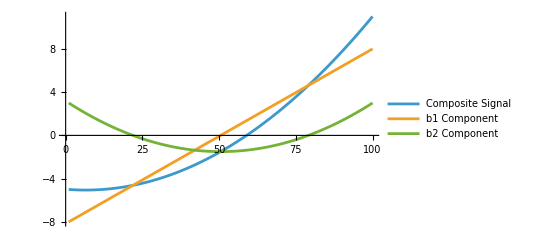

```mathematica
ClearAll["Global`*"]

(* 1. THE TIME VECTOR (For Legendre, we usually evaluate from -1 to 1) *)
Npts = 100;
t = Table[k, {k, -1.0, 1.0, 2.0/(Npts - 1)}];

(* 2. THE SIGNAL *)
signal = 8*(t) + 3*(1.5*t^2 - 0.5);

(* 3. THE BASIS VECTORS (Stripped from the signal) *)
b1 = t;
b2 = 1.5*t^2 - 0.5;

(* 4. ORTHOGONALITY CHECK *)
Print["--- ORTHOGONALITY ---"];
(* We use Chop to ignore microscopic rounding errors *)
Print["b1 . b2 = ", Chop[b1 . b2]]; 

(* 5. CALCULATE PROJECTIONS (This only works because the step above was 0!) *)
c1 = Chop[(signal . b1) / (b1 . b1)];
c2 = Chop[(signal . b2) / (b2 . b2)];

Print["\n--- COEFFICIENTS ---"];
Print["Amount of b1 (Expected 8): ", c1];
Print["Amount of b2 (Expected 3): ", c2];

(* 6. VISUAL PROOF *)
ListLinePlot[{signal, c1*b1, c2*b2}, 
  PlotLegends -> {"Composite Signal", "b1 Component", "b2 Component"}]
```